## Mathematica Basics

### Assignments

```mathematica
x=2
```

2

```mathematica
x
```

2

```mathematica
y=3
```

3

```mathematica
x=4
```

4

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
DiceRoll1=Ceiling[Random[]*6]
```

2

```mathematica
DiceRoll1
```

2

```mathematica
DiceRoll2:=Ceiling[Random[]*6]
```

```mathematica
DiceRoll2
```

2

```mathematica
DiceRoll2
```

1

### Functions

```mathematica
Cos[2];
```

```mathematica
N[Cos[2]]
```

-0.416147

```mathematica
N[Cos[2],100]
```

-0.4161468365471423869975682295007621897660007710755448907551499737819649361240791690745317778601691404

```mathematica
F1[x_]:=Cos[x]
```

```mathematica
F1[2]
```

Cos[2]

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

```mathematica
F2[x_]:=Integrate[Cos[x],x]
```

```mathematica
F2[2]
```

Integrate::ilim: Invalid integration variable or limit(s) in 2.

∫Cos[2]ⅆ2

```mathematica
F3[x_]=Integrate[Cos[x],x]
```

Sin[x]

```mathematica
F3[2]
```

Sin[2]

```mathematica
myPlot=Plot[F3[x],{x,0,1}];
```

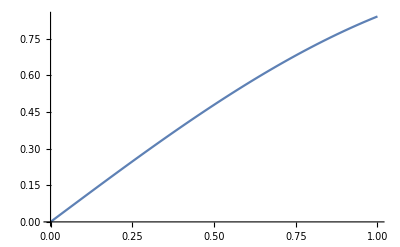

```mathematica
Show[myPlot]
```

### Arrays

```mathematica
myArray={0,1,2,3}
```

{0,1,2,3}

```mathematica
myArray[[2]]
```

1

```mathematica
myArray[[2]]=10;
myArray
```

{0,10,2,3}

```mathematica
myArray=Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

### Loops

```mathematica
For[i=1,i≤10,i++,
Print[i];
]
```

1

2

3

4

5

6

7

8

9

10

```mathematica
For[i=1,i≤10,i++,
If[i==5,Print[i]];
]
```

5

### Replacement Rules

```mathematica
F4[x_]:=A Sin[k x]
A=1;
k=1;
```

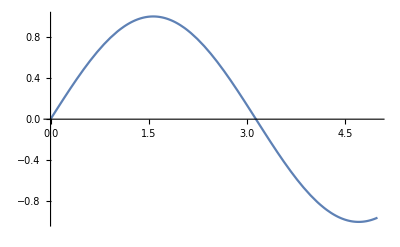

```mathematica
Plot[F4[x],{x,0,5}]
```

```mathematica
F4[x]
```

Sin[x]

```mathematica
Clear[A,k]
```

```mathematica
F4[x]
```

A Sin[k x]

```mathematica
sub={A->1,k->1}
```

{A→1,k→1}

```mathematica
Plot[F4[x]/.sub,{x,0,5}]
```

-Graphics-

```mathematica
F4[x]
```

A Sin[k x]